```mathematica
f[x_,y_]=((x+1)^2)^(1/3)+((y-3)^2)^(1/3)-4

g[x_,y_]=3 x^2-5 y^2-15
```

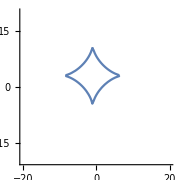

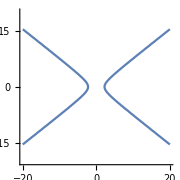

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-20,20},{y,-20,20},Axes->True,Frame->False,ImageSize->Small]
gr2=ContourPlot[g[x,y]==0,{x,-20,20},{y,-20,20},Axes->True,Frame->False,ImageSize->Small]
```

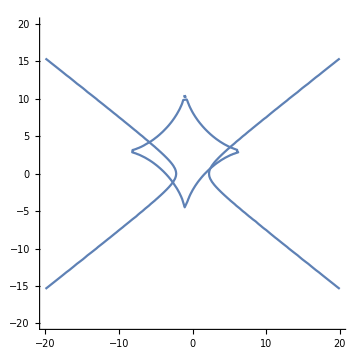

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-3},{y,1}]
```

{x→-2.68587,y→-1.15253}

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,4},{y,-1}]
```

{x→2.42671,y→0.730304}